# Photorecombination continuum

## Theoretical calculation

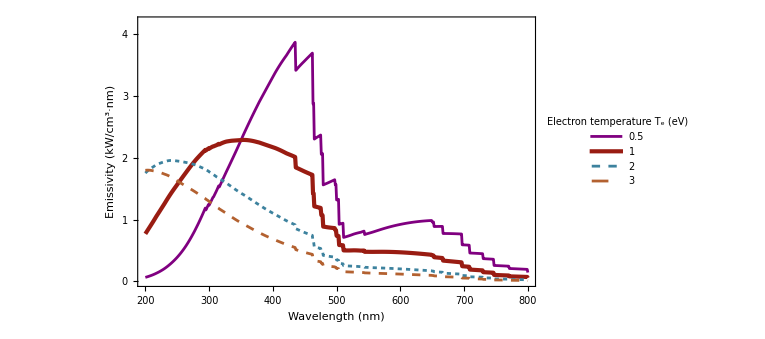

```mathematica
(* -- constants and units -- *)
ne=1*^19; (* electron density [cm^-3] *)
ni=ne; (* ion density [cm^-3], ionization order ~ 1 *)

eV=1/1.60218*^-19; (* unit conversion [eV/J] *)
h=6.62607*^-34 eV; (* [eV·s] *)
c=2.99792458*^17; (* [nm/s] *)
mec2=9.10938*^-31 c^2/10^18 eV; (* electron rest mass [eV] *)
unit=10^-7/eV; (* unit conversion [eV/cm^4]->[J/(cm^3·nm)] *)

arii=15.76; (* Ar II ground state [eV] *)

(* -- recombined states -- *)
config={"4s","4p","3d"};
{cs,stat}=Table[
Import[NotebookDirectory[]<>dir<>"/"<>config[[i]]<>".mx"],
{dir,{"cross section","states"}},{i,Length[config]}];
raw=Table[stat[[i]]ᵀ,{i,Length[stat]}]ᵀ;
{g,th}={raw[[1]],arii-raw[[2]]};

(* -- cross section -- *)
csInterp=Map[Interpolation[#,InterpolationOrder->2]&,cs];
σiz[λ_,n_,i_]:=Piecewise[
{{csInterp[[n]][λ],λ≤h c/th[[n,i]]},
{0,λ>h c/th[[n,i]]}}];

(* -- emissivity -- *)
ϵ[λ_:400(*[nm]*),Te_:1(* [eV] *)]:=
Sum[Sum[
ni ne g[[n,i]]/Total[g[[n]]] σiz[λ,n,i] 1/h √(2/π)(1/mec2)^(3/2)(1/Te)^(3/2)(h c/λ)^5 Exp[-((h c/λ)-th[[n,i]])/Te] unit,
{i,Length[g[[n]]]}],{n,Length[g]}]; (* [W/(cm^3·nm)] *)

(* -- data -- *)
wl=Range[200,800,1];
temp={.5,1,2,3};
ϵc=ParallelTable[Quiet@(ϵ[λ,Te]),{Te,temp},{λ,wl}]; (* calculated emissivity *)
dt=Transpose[{wl,#}&/@ϵc,{1,3,2}];

(* -- filter -- *)
(*σ=.5; (* std of Gaussian filter *)
ϵf=Map[GaussianFilter[#,2σ]&,ϵc]; (* filtered *)
dt=Transpose[{wl,#}&/@ϵf,{1,3,2}];*)

(* -- plot -- *)
gf=ListLinePlot[

(* -- data -- *)
dt,

Joined->True,
ScalingFunctions->"Linear", 

PlotRange->{{200,800},{0,4200}},
PlotRangePadding->0,
PlotRangeClipping->True,

LabelStyle->{FontFamily->"Helvetica",FontSize->14,FontWeight->Plain}, 

PlotStyle->{
{Purple,AbsoluteThickness[2]},
{RGBColor[.60,.11,.07,1],AbsoluteThickness[3]},
{RGBColor[.24,.51,.62,1],AbsoluteThickness[2],AbsoluteDashing[3]},
{RGBColor[.7,.38,.19,1],AbsoluteThickness[2],AbsoluteDashing[6]}
},

PlotLegends->Placed[
LineLegend[
ToString[#]&/@temp,
LegendMarkerSize->{{40,10}},
LabelStyle->{Black,FontFamily->"Helvetica", FontSize->14},
LegendLabel->StringForm["Electron temperature `1` (eV)\n",Subscript[Style["T",Italic],"e"]],
LegendFunction->(Framed[#,Background->Transparent,FrameStyle->Directive[Black,AbsoluteThickness[1]]]&),
LegendMarkers->None,
LegendMargins->0,
LegendLayout->{"Column",2}], 
{Scaled@{.95,.92},{1,1}}],

Frame->True,
FrameTicks->{
{Table[{i*100,If[Mod[i,5]==0,i/10,Null],{If[Mod[i,5]==0,.015,.008],0}},{i,0,40,2}],
Table[{i*100,Null,{If[Mod[i,5]==0,.015,.008],0}},{i,0,40,2}]},
{Table[{i,If[Mod[i,100]==0,i,Null],{If[Mod[i,100]==0,.015,.008],0}},{i,200,800,20}],
Table[{i,Null,{If[Mod[i,100]==0,.015,.008],0}},{i,200,800,20}]}
},
FrameLabel->{{"Emissivity (kW/cm^3·nm)",None},{"Wavelength (nm)",None}},
FrameStyle->Directive[Black,AbsoluteThickness[1]],

GridLines->None,
ImagePadding->{{35,15},{40,10}},
ImageSize->(100*2)*(72/25.4),
AspectRatio->.6

];

Print[gf];

Export[NotebookDirectory[]<>"continuum.pdf",gf];
```